# Pokrytí dat RBF sítí Demonstrace pokrytí vstupních dat složitější RBF sítí.

## Načtení knihovny NeuralNetworks

Nejdříve načteme knihovnu neuronových sítí.

```mathematica
<< NeuralNetworks`
```

Pokud pracujete v Mathematice 8.0, vypněte ještě zobrazování chybové hlášky Remove::rmnsm. Tuto hlášku vyhazují funkce knihovny NeuralNetworks. Na funkci knihovny toto nemá žádný vliv.

```mathematica
Off[Remove::rmnsm]
```

## Příprava trénovacích dat

Pokrytí dat budeme předvádět na klasifikaci do dvou tříd. Data budeme mít jednoduchá dvoudimenzionální, každá třída dat se skládá ze třech dobře oddělených, shluků. Shluky se vzájemně nepřekrývají.
Vygenerujeme tyto data.

```mathematica
values=10;
cluster1x =RandomReal[{7,6},{values,1}];cluster1y=RandomReal[ {11,12},{values,1}];
cluster2x =RandomReal[{-4,-5},{values,1}];cluster2y=RandomReal[ {9,10},{values,1}];
cluster3x =RandomReal[{0,-1},{values,1}];cluster3y=RandomReal[ {12,13},{values,1}];
cluster1=Join[cluster1x,cluster1y,2];
cluster2=Join[cluster2x,cluster2y,2];
cluster3=Join[cluster3x,cluster3y,2];
inDataClass1 = Join[cluster1,cluster2,cluster3];
cluster4x =RandomReal[{2,1},{values,1}];cluster4y=RandomReal[ {4,5},{values,1}];
cluster5x =RandomReal[{-3,-4},{values,1}];cluster5y=RandomReal[ {12,13},{values,1}];
cluster6x =RandomReal[{9,8},{values,1}];cluster6y=RandomReal[ {10,9},{values,1}];
cluster4=Join[cluster4x,cluster4y,2];
cluster5=Join[cluster5x,cluster5y,2];
cluster6=Join[cluster6x,cluster6y,2];
inDataClass2 = Join[cluster4,cluster5,cluster6];
inData= Join[inDataClass1,inDataClass2];
outClass1=ConstantArray[{1,0},{3*values}];outClass2 = ConstantArray[{0,1},{3*values}];
outData= Join[outClass1,outClass2];
```

Takto vypadají naše vynerovaná vstupní data. Můžeme je chápat jako seznam bodů, které jsou určeny svými {x,y} souřadnicemi.

```mathematica
inData
```

{{6.59119,11.457},{6.94346,11.8921},{6.39805,11.8472},{6.50084,11.9287},{6.42161,11.8483},{6.81109,11.1162},{6.921,11.947},{6.13438,11.3726},{6.42969,11.8733},{6.47113,11.3003},{-4.37532,9.43502},{-4.82214,9.68536},{-4.91444,9.21264},{-4.6855,9.05775},{-4.05781,9.48972},{-4.52468,9.08726},{-4.11492,9.60642},{-4.10235,9.36585},{-4.90184,9.3778},{-4.55569,9.67004},{-0.111546,12.753},{-0.000993331,12.688},{-0.498038,12.9651},{-0.653784,12.7139},{-0.776364,12.5391},{-0.656307,12.9788},{-0.688571,12.468},{-0.885478,12.2093},{-0.633573,12.3304},{-0.512597,12.7819},{1.74633,4.08469},{1.51477,4.68415},{1.74442,4.08876},{1.57605,4.95476},{1.32507,4.83008},{1.78062,4.4587},{1.04028,4.74185},{1.08041,4.86378},{1.66306,4.13069},{1.58167,4.24892},{-3.19894,12.2015},{-3.16516,12.5445},{-3.75025,12.7495},{-3.03146,12.7495},{-3.73064,12.226},{-3.63128,12.4042},{-3.64043,12.1656},{-3.76752,12.5417},{-3.48316,12.6141},{-3.94582,12.6873},{8.86901,9.8304},{8.61326,9.05712},{8.4613,9.30815},{8.87554,9.10793},{8.10527,9.2356},{8.45479,9.30648},{8.62085,9.97059},{8.95018,9.02425},{8.79651,9.00626},{8.39712,9.34221}}

A takto vypadají data výstupní.

```mathematica
outData
```

{{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{1,0},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1},{0,1}}

Vygenerovaná data si můžeme pro lepší představu zobrazit. Každá třída dat je v grafu zobrazena jinou barvou.

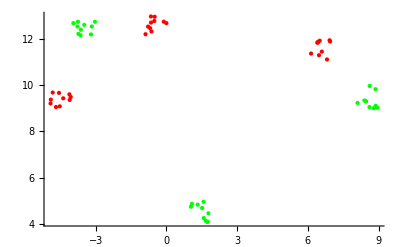

```mathematica
ListPlot[{inDataClass1,inDataClass2},PlotStyle->{Red,Green}]
```

Po vygenerování dat můžeme začít učit síť.

## Učení RBF sítě

Tato jednoduchá data budeme chtít klasifikovat pomocí RBF sítě se třemi RBF neurony, dvěma vstupy a dvěma výstupními neurony.
Vytvoříme RBF síť podle popisu výše.

```mathematica
net=InitializeRBFNet[inData,outData,3,LinearPart->False,OutputNonlinearity->Sigmoid]
```

RBFNet[{{w1, λ, w2}},{Neuron → Exp, FixedParameters → None, AccumulatedIterations → 0, CreationDate → {2011, 3, 29, 12, 40, 3.5158149}, OutputNonlinearity → Sigmoid, NumberOfInputs → 2}]

Zobrazíme si informace o sítí. Tím se ujistíme že síť je opravdu taková jakou jsme popsali.

```mathematica
NetInformation[net]
```

Radial Basis Function network. Created 2011-3-29 at 12:40. The network has 2 inputs and 2 outputs.  It consists of 3 basis functions of Exp type. There is a nonlinearity at the output of type Sigmoid.

Naučíme vytvořenou síť na našich datech.

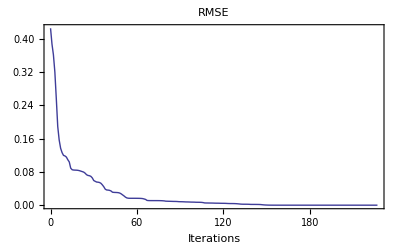

```mathematica
{net2,record}=NeuralFit[net,inData,outData,350,ReportFrequency->20];
```

## Výstup neuronové sítě

Podívejme se jak neuronová síť pokrývá jednotlivé třídy dat. Nejprve si zobrazíme výstup pro červenou třídu. Oblast grafu ohraničená červenou čarou určuje oblast dat, kterou neuronová síť klasifikuje do červené třídy. Tato oblast odpovídá datům, pro které první výstupní neuron vrací hodnotu větší než 0.5.

```mathematica
out1=Plot3D[net2[{x,y}][[1]],{x,-10,10},{y,0,30},PlotRange->All,PlotStyle->Opacity[0.2]];
inDataClass13d2=inDataClass1/.{x_?NumberQ,y_?NumberQ}:>{x,y,0};
inDataClass23d2=inDataClass2/.{x_?NumberQ,y_?NumberQ}:>{x,y,0};
data3d2=ListPointPlot3D[{inDataClass13d2,inDataClass23d2},PlotStyle->{{PointSize[Large],Red},{PointSize[Large],Green}},PlotStyle->PointSize[Large]];
out1true=Plot3D[net2[{x,y}][[1]],{x,-10,10},{y,0,30},PlotRange->All,PlotStyle->Opacity[0.7], RegionFunction->Function[{x,y,z},z>0.5],BoundaryStyle->Directive[Red,Thick]];
Show[out1,out1true,data3d2]
```

-Graphics3D-

Obdobně si zobrazíme výstup pro zelenou třídu. Oblast grafu ohraničená zelenou čarou určuje oblast dat, kterou neuronová síť klasifikuje do zelené třídy. Tato oblast odpovídá datům, pro které první výstupní neuron vrací hodnotu větší než 0.5.

```mathematica
out2true=Plot3D[net2[{x,y}][[2]],{x,-10,10},{y,0,30},PlotRange->All,PlotStyle->Opacity[0.7], RegionFunction->Function[{x,y,z},z>0.5],BoundaryStyle->Directive[Green,Thick],Mesh->None];
out2=Plot3D[net2[{x,y}][[2]],{x,-10,10},{y,0,30},PlotRange->All,PlotStyle->Opacity[0.2]];
Show[out2true,out2,data3d2]
```

-Graphics3D-

Obdobný výstup klasifikace pomocí neuronové sítě. Do 2D jsou promítnuty hraniční přímky. Po ukázání na hraniční přímku se ukáže výstup sítě ve formě vzorce.

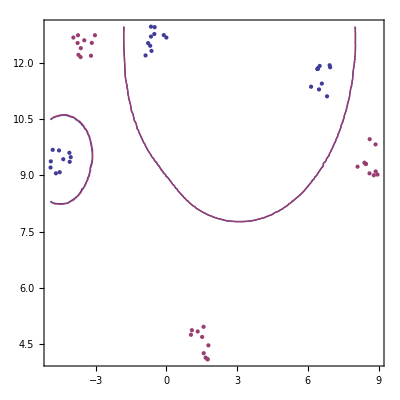

```mathematica
NetPlot[net2,inData,outData, DataFormat->Classifier]
```

## Výstup RBF neuronů

Nyní se podíváme na “vnitřnosti” neuronové sítě. Nejprve si zobrazíme výstup všech tří RBF neuronů. Abychom se dostali k výstupu RBF neuronů musíme upravit strukturu sítě obdobně jako u ukázkového příkladu sítě s jedním neuronem. Připojíme tedy každý RBF neuron přímo na výstupní neuron s vahou 1. Na výstupních neuronech se tedy zobrazí přímo výstupy z RBF neuronů.

Schéma původní sítě:   -Graphics-

Schéma upravené sítě:-Graphics-

Provedeme popsané změny.

```mathematica
net3=net2;(*nechceme si rozbít původní síť*)
net3[[1,1,3]]=Append[IdentityMatrix[3],{0,0,0}];(*nastaveni vystupni vrstvy*)
NetInformation[net3]
```

Radial Basis Function network. Created 2011-3-29 at 12:40. The network has 2 inputs and 3 outputs.  It consists of 3 basis functions of Exp type. There is a nonlinearity at the output of type Sigmoid.

A zobrazíme výstup RBF neuronů.

```mathematica
gauss1=Plot3D[net3[{x,y}][[1]],{x,-10,10},{y,0,25},PlotRange->All];
gauss2=Plot3D[net3[{x,y}][[2]],{x,-10,10},{y,0,25},PlotRange->All];
gauss3=Plot3D[net3[{x,y}][[3]],{x,-10,10},{y,0,25},PlotRange->All];
Show[gauss1,gauss2,gauss3]
```

-Graphics3D-

Výstup může mít více podob, je závislý na tom jak se neuronová síť naučila data. Pokud vidíte pouze jednu gaussovu funkci, je možné, že ostatní jsou “pod” ní. Následující průhůedné zobrazení s daty to objasní.

Přidáme do grafu ještě vstupní data pro lepší představu o jejich pokrytí (levé tlačítko myši otáčí grafem).

```mathematica
inDataClass13d=inDataClass1/.{x_?NumberQ,y_?NumberQ}:>{x,y,0.50};
inDataClass23d=inDataClass2/.{x_?NumberQ,y_?NumberQ}:>{x,y,0.50};
gauss0O=Plot3D[net3[{x,y}][[1]],{x,-10,10},{y,0,25},PlotRange->All,PlotStyle->Opacity[0.4]];
gauss1O=Plot3D[net3[{x,y}][[2]],{x,-10,10},{y,0,25},PlotRange->All,PlotStyle->Opacity[0.4]];
gauss2O=Plot3D[net3[{x,y}][[3]],{x,-10,10},{y,0,25},PlotRange->All,PlotStyle->Opacity[0.4]];
data3d=ListPointPlot3D[{inDataClass13d,inDataClass23d},PlotStyle->{{PointSize[Large],Red},{PointSize[Large],Green}},PlotStyle->PointSize[Large]];
Show[gauss0O,gauss1O,gauss2O,data3d]
```

-Graphics3D-

## Prohlášení

Tento text je vypracován jako součást bakalářské práce Adama Činčury “Demonstrační aplikace pro podporu kurzu neuronových sítí” na FEL ČVUT 2011.